Define the distributions

```mathematica
kappaDist=n0(π (κ - 1/2) vth^2)^(-1/2)Gamma[κ+1]/Gamma[κ+1/2](1+v^2/((κ-1/2)vth^2))^(-(κ+1));
```

```mathematica
maxwellDist=n0(π vth^2)^(-1/2)Exp[-v^2/vth^2];
```

Integrals

#### Zeroth moment of the kappa dist and Maxwellian dist, just to see

```mathematica
Integrate[kappaDist,{v,-∞,∞},Assumptions->vth>0&&κ>1/2]
```

n0

```mathematica
Integrate[maxwellDist,{v,-∞,∞},Assumptions->vth>0]
```

n0

#### Second moment of the kappa distribution

```mathematica
Integrate[v^2 kappaDist,{v,-∞,∞},Assumptions->vth>0&&κ>1/2]
```

(n0 vth^2)/2

#### Now try the Baumjohann & Treumann integral (Equation (10.31), maybe?) This isn’t exact, but for example …

```mathematica
Integrate[(1-2ⅈ v-3 v^2)kappaDist,{v,-∞,∞},Assumptions->vth>0&&κ>1/2]
```

n0-(3 n0 vth^2)/2

Plot the distributions (specify kappa vals to plot with plotKappaVals list)

For the 1-D kappa distribution, the theoretical minimum is κ = 0.5. (In d dimensions the minimum is κ = d/2.) 
There is good experimental evidence suggesting that κ_t ≅ 0.95 + d/2 marks a transition between plasmas that are far from thermal equilibrium (κ < κ_t) and those that are near thermal equilibrium (κ > κ_t)

```mathematica
plotKappaVals={0.6,0.8,1.45,5};
```

#### Define functions to plot using units such that vth = 1 and n0 = 1

```mathematica
plotFuncs=(((kappaDist/.{κ->#})&/@plotKappaVals)~Join~{maxwellDist})/.{vth->1,n0->1}
```

{1.67566/((1+10. v^2)^1.6),1.06899/((1+3.33333 v^2)^1.8),0.758623/((1+1.05263 v^2)^2.45),(256 √2)/(189 π (1+(2 v^2)/9)^6),(ⅇ^(-v^2))/(√π)}

#### Define plot labels

```mathematica
plotLabelStrings=(StringForm["κ = `1`",#]&/@plotKappaVals)~Join~{"Maxwellian"};
```

```mathematica
plotLabels=Style[#,Bold,FontSize->16]&/@plotLabelStrings;
```

#### Linear plot

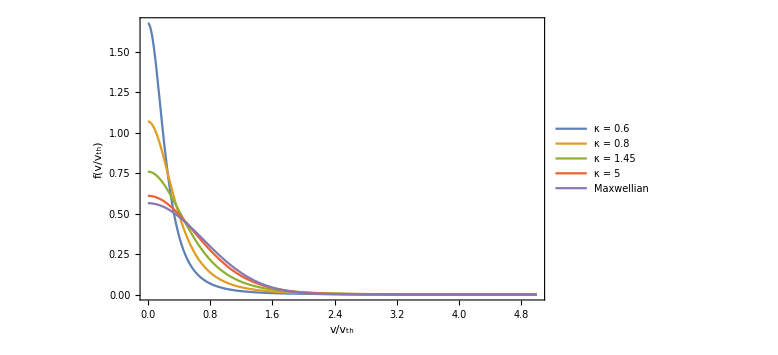

```mathematica
Plot[plotFuncs,{v,0,5},PlotRange->Full,
(*PlotLabels->Placed[(StringForm["κ = `1`",#]&/@plotKappaVals),Top],*)
PlotLegends->plotLabels,
Frame->True,FrameLabel->{"v/v_th","f(v/v_th)"},FrameStyle->Directive[FontSize->16,Black,Bold],
ImageSize->Large]
```

#### Log-log plot to show the power-law tails that characterize kappa distributions

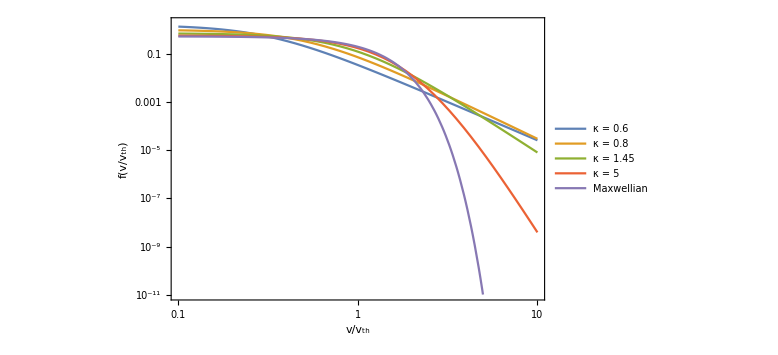

```mathematica
LogLogPlot[plotFuncs,{v,0.1,10},PlotRange->{{0.1,10},{10^-11,2}},
(*PlotLabels->Placed[(StringForm["κ = `1`",#]&/@plotKappaVals),Top],*)
PlotLegends->plotLabels,
Frame->True,FrameLabel->{"v/v_th","f(v/v_th)"},FrameStyle->Directive[FontSize->16,Black,Bold],
ImageSize->Large]
```

Derivative of 1-D kappa dist, growth/damping rate

```mathematica
D[kappaDist,v]/kappaDist
```

(2 v (-1-κ))/(vth^2 (1+v^2/(vth^2 (-1/2+κ))) (-1/2+κ))

The actual damping rate!

```mathematica
LangdampPerOmegapeMaxwellian[k_,lambdaD_]:=-(π/8)^(1/2)1/(k^3 lambdaD^3)Exp[-1/(2 k^2 lambdaD^2)-3/2];
```

```mathematica
LangdampPerOmegapeKappa[k_,lambdaD_,kappa_]:=-(π/8)^(1/2)1/(k^3 lambdaD^3)(kappa+1)/(kappa-1/2)^(3/2)Gamma[kappa+1]/Gamma[kappa+1/2](1+(1/(k^2 lambdaD^2)+3)/(2 (kappa-1/2)))^(-(kappa+2));
```

```mathematica
(LangdampPerOmegapeMaxwellian[#,1]&/@{0.1,1,10,100,1000})//N
```

{-2.6969×10^-20,-0.0848088,-0.000139129,-1.39819×10^-7,-1.39826×10^-10}

```mathematica
kappaVals=Reverse@{0.52,0.6,0.8,1.45,5};
```

```mathematica
PlotFuncs={Abs@LangdampPerOmegapeMaxwellian[k,1],Abs[LangdampPerOmegapeKappa[k,1,#]]&/@kappaVals};
```

```mathematica
legendNames=Style[#,FontSize->16]&/@({"Maxwellian"}~Join~(ToString@StringForm["κ = `1`",#]&/@kappaVals))
```

{Maxwellian,κ = 5,κ = 1.45,κ = 0.8,κ = 0.6,κ = 0.52}

```mathematica
mink=0.02;
maxk=15;
```

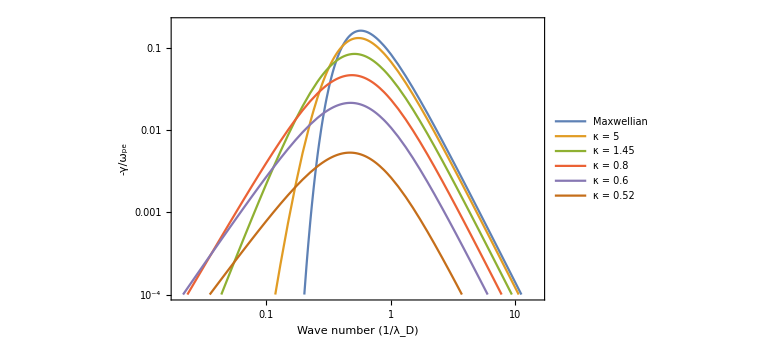

```mathematica
LogLogPlot[Evaluate[PlotFuncs],{k,mink,maxk},PlotLegends->legendNames,PlotRange->{{mink,maxk},{1*^-4,0.2}},ImageSize->Large,Frame->True,FrameLabel->{"Wave number (1/λ_D)","-γ/ω_pe"},FrameStyle->Directive[FontSize->18]]
```

### Example slope calculation

```mathematica
x1=0.0358;
x2=0.137;
y1=1*^-4;
y2=0.00146;
slope=(Log[y2]-Log[y1])/(Log[x2]-Log[x1])
```

1.99773

### Get slope for a large number of kappa values

```mathematica
kappaVals=Range[0.51,20,0.25];
```

```mathematica
PlotFuncs=Abs[LangdampPerOmegapeKappa[k,1,#]]&/@kappaVals;
```

```mathematica
slopes=((Log[((PlotFuncs)/.k->0.1)]-Log[((PlotFuncs)/.k->0.01)])/(Log[0.1]-Log[0.01]))
```

{1.9879,2.47895,2.969,3.45805,3.9461,4.43316,4.91924,5.40435,5.88849,6.37167,6.85389,7.33516,7.8155,8.2949,8.77337,9.25092,9.72755,10.2033,10.6781,11.152,11.625,12.0972,12.5685,13.0388,13.5084,13.977,14.4448,14.9118,15.3779,15.8431,16.3076,16.7711,17.2339,17.6959,18.157,18.6173,19.0768,19.5355,19.9934,20.4506,20.9069,21.3625,21.8172,22.2712,22.7245,23.1769,23.6287,24.0796,24.5298,24.9793,25.428,25.876,26.3232,26.7697,27.2155,27.6606,28.105,28.5486,28.9915,29.4338,29.8753,30.3161,30.7562,31.1957,31.6344,32.0725,32.5099,32.9466,33.3827,33.818,34.2527,34.6868,35.1202,35.5529,35.985,36.4164,36.8472,37.2774}

```mathematica
line=Fit[slopeKappa,{1,x},x]
```

1.45997+1.83139 x

```mathematica
slopeKappa=Partition[Riffle[kappaVals,slopes],2];
```

```mathematica
Show[Plot[Legended[line,Style["Best Fit (1.83κ+1.46)",Directive[Black,FontSize->16]]],{x,0.5,5},PlotStyle->Directive[Gray],Frame->True,FrameLabel->{"κ","a(κ)"},FrameStyle->Directive[Black,FontSize->18],ImageSize->Medium],ListPlot[Legended[slopeKappa,Style["Calculated",Directive[Black,FontSize->16]]],PlotMarkers->"+",PlotStyle->Directive[Black]]]
```

-Graphics-